## Phases and Coefficiets

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
ClearAll[n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList,k1A,k2A,a1A,a2A,range,range2];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

Parameters

```mathematica
thetamV=Pi/5;
k1V=0.3;
k2V=0.7;
a1V=0.1(k1V)^(-5/3);
a2V=0.1(k1V)^(-5/3);
phi1V=0;
phi2V=0;
```

Building Functions

Test result for some example data.

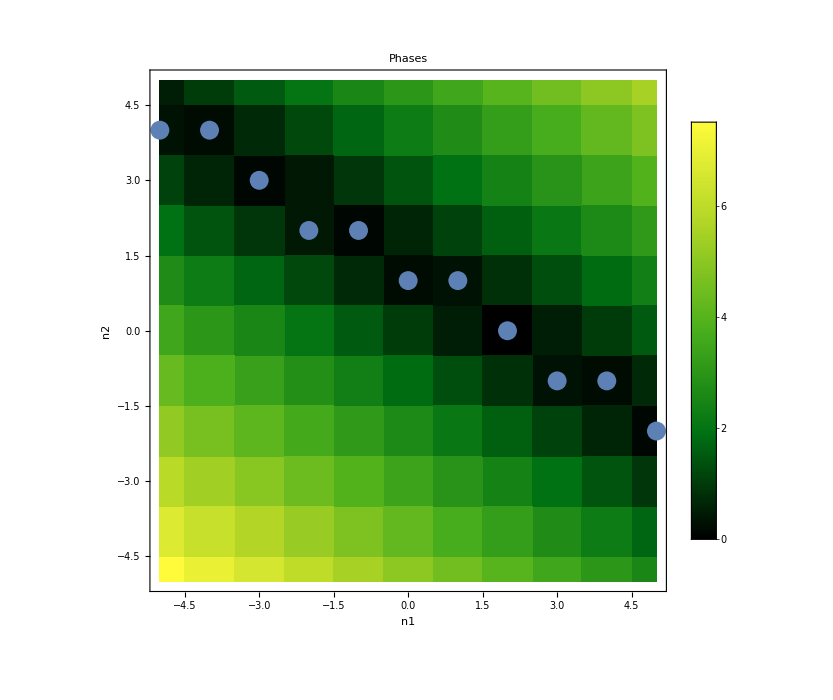
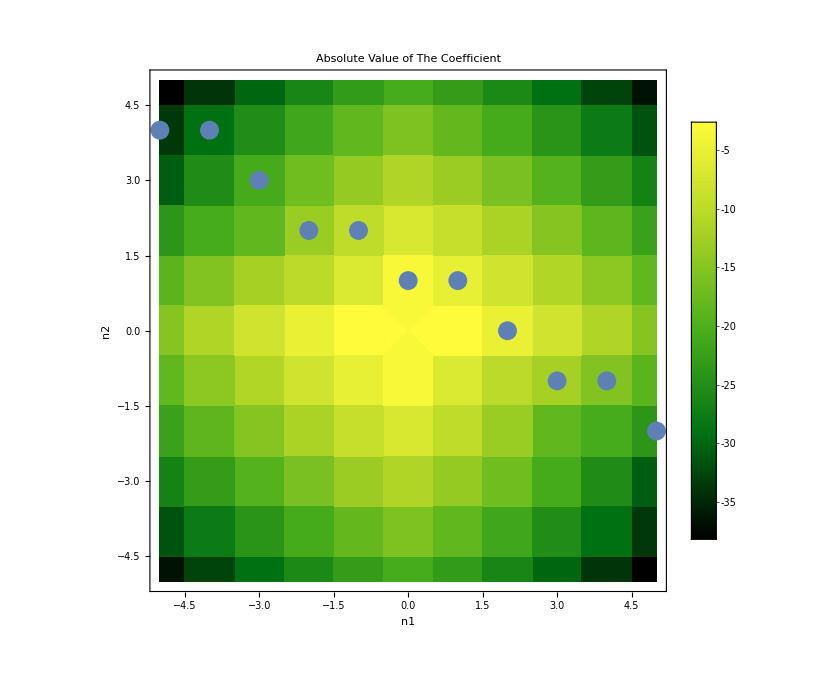
-Graphics- | -Graphics-
-Graphics- | -Graphics-
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2,order,endpoint},
k1A=0.5;
k2A=0.8;
a1A=0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5;
order=5;
endpoint=800;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
},{
Table[Show[pltN[k1A,k2A,a1A,a2A,thetamA,endpoint,Red],plt0Orders[k1A,k2A,a1A,a2A,thetamA,endpoint,ord,0,ToString[ord]<>",0;",Black](*,pltAll[k1,k2,a1,a2,order,Magenta]*),PlotRange->All],{ord,0,order}]
}
}]
]
(*Export["export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png",%]*)
```

## Compare with Previous calculations

We had a case where adding 1 and 2 will change the result but adding 3 doesn’t. They match the exact data when 4th order is added.

### First Case

k1=0.3;
k2=0.99;
a1=0.2*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

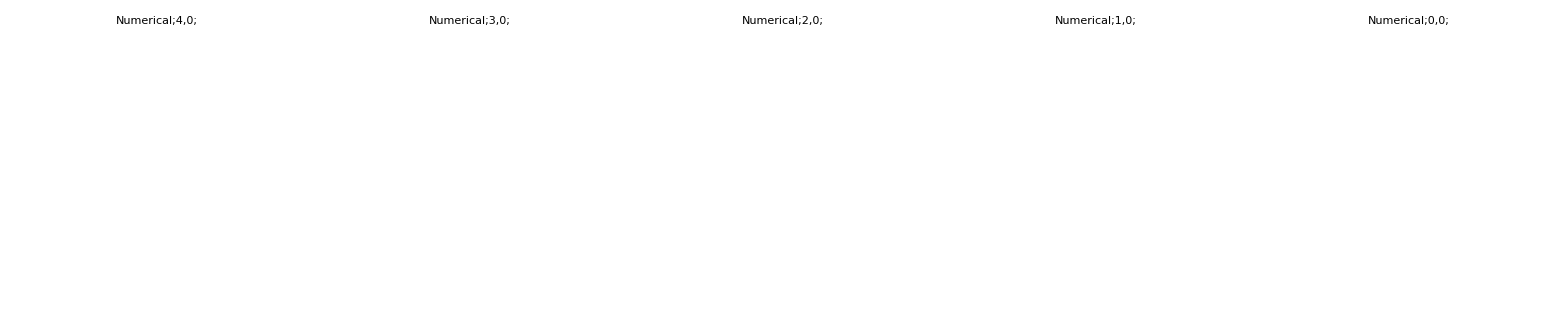

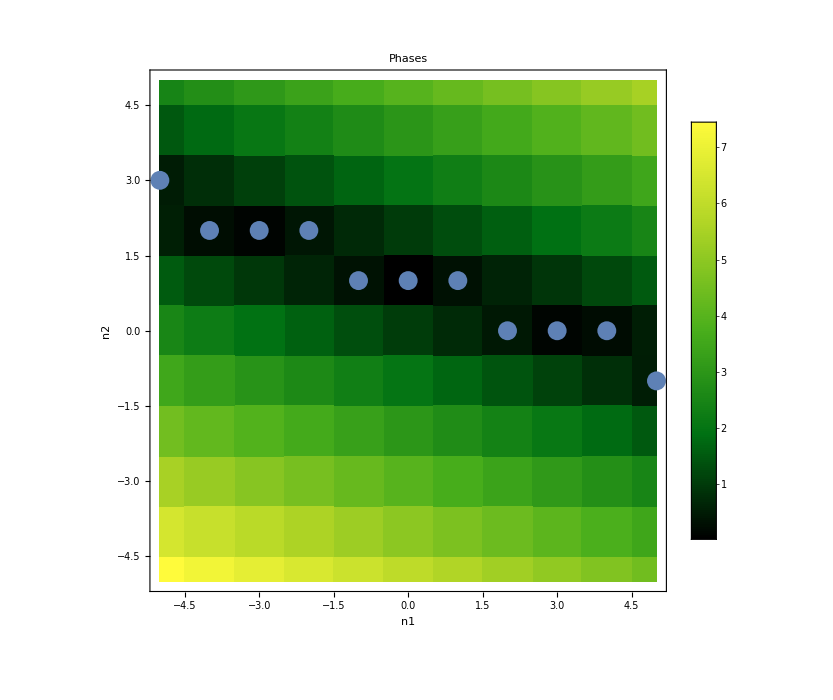
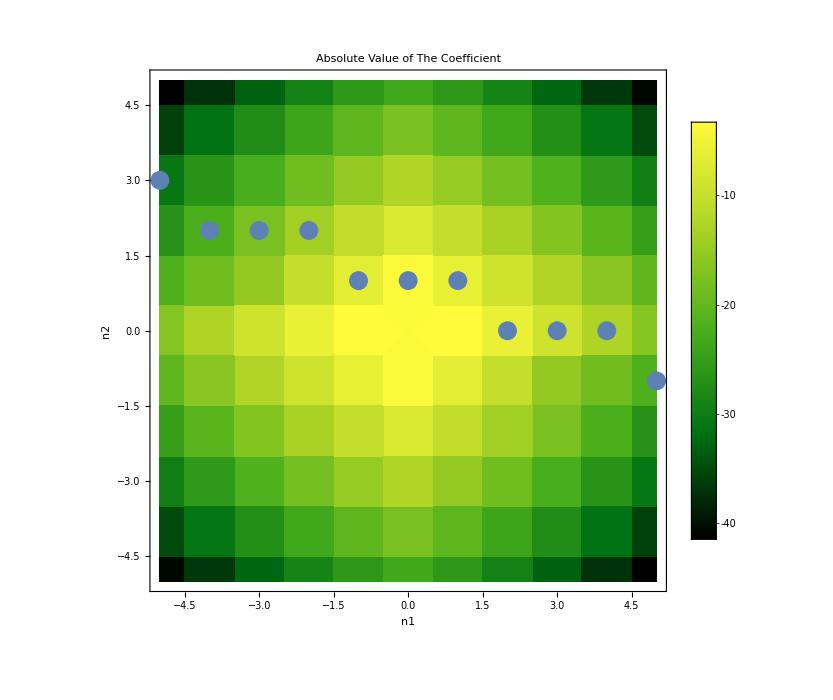
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.2*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

### Second Case

k1=0.3;
k2=0.99;
a1=0.4*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

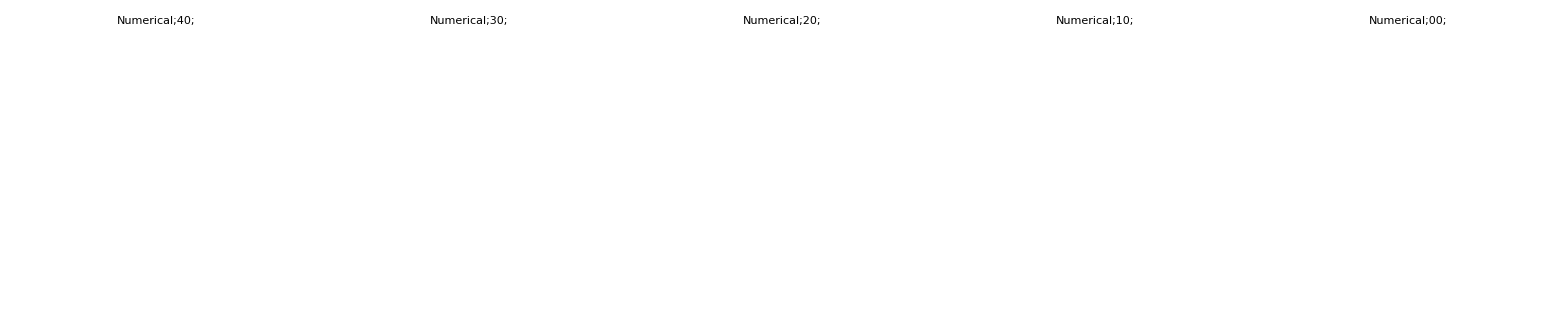

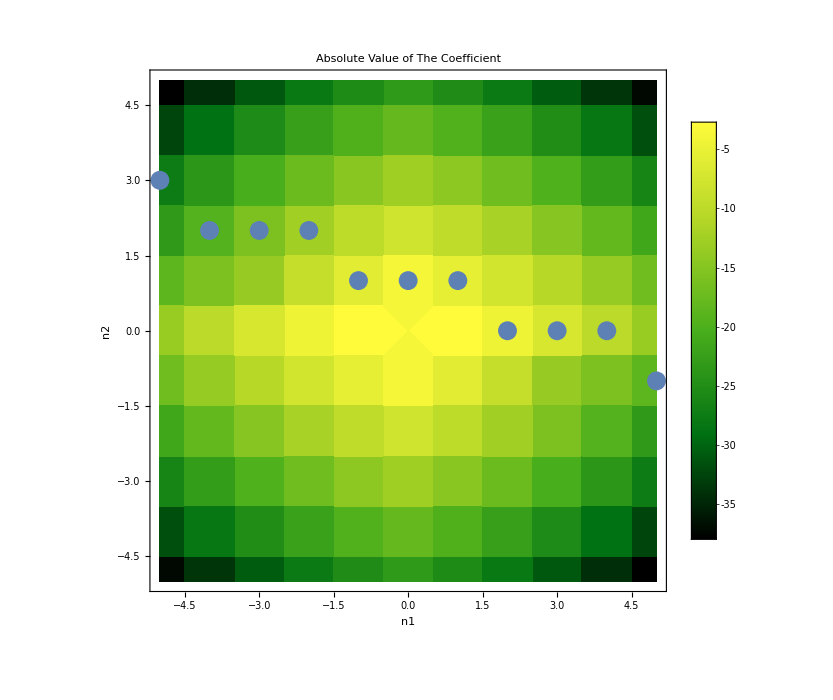
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.4*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

#### Resonances